```mathematica
(*define model*)
jX=(jXm X)/(X+KX);
 jN=(jNm Ν)/(Ν+KN);
jHT=j0HT;
rNH=σNH nNH jHT;
rNS=σNS nNS j0ST;
jX=(jXm X)/(X+KX);
 jN=(jNm Ν)/(Ν+KN);
jHT=j0HT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jL=A L astar;
jST=j0ST(1+b cROS1);
(*SU: synthesising units*)
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);
(*full set of fluxes, in form {flux name, formula}*)
tsolve={
{jHG,F[jHGm][yC (ρC S/H+jX),(jN+nNX jX+rNH)nNH^-1]},
{ρN,jN+nNX jX+rNH-nNH jHG yN^-1},
{jeC,jX+ρC S/H-jHG yC^-1},
{jCO2,kCO2 jeC},
{rCH,σCH(jHT+(1-yC)jHG yC^-1)},
{rCS,σCS(j0ST+(1-yC)jSG yC^-1)},
{jCP,F[jCPm][yCL jL,(jCO2+rCH) H/S+rCS](cROS1+1)^-1},
{jeL,jL-jCP yCL^-1},
{jNPQ,(kNPQ^-1+jeL^-1)^-1},
{cROS1,(jeL-jNPQ)/kROS},
{jSG,F[jSGm][yC jCP,(ρN H/S+rNS)nNS^-1]},
{ρC,jCP-jSG yC^-1}
};
(*labels for fluxes: for plotting*)
names={jHG->"j_HG",ρN->"ρ_N",jeC->"j_eC",jCO2->"j_CO_2",rCH->"r_CH",rCS->"r_CS",jCP->"j_CP",jeL->"j_eL",jNPQ->"j_NPQ",cROS1->"c_ROS",jSG->"j_SG",ρC->"ρ_C"};
(*get the adjacency matrix*)
matrix=Table[FreeQ[row[[2]],x],{row,tsolve},{x,tsolve[[All,1]]}]/.{True->0,False->1};
(*show the matrix*)
(Export[NotebookDirectory[]<>"adjacency-matrix-corals.pdf",#];#)&@TableForm[matrix,TableHeadings->{#,#}&@(tsolve[[All,1]]/.names)]
```

| j_HG | ρ_N | j_eC | j_CO_2 | r_CH | r_CS | j_CP | j_eL | j_NPQ | c_ROS | j_SG | ρ_C
j_HG | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
ρ_N | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j_eC | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
j_CO_2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
r_CH | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
r_CS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
j_CP | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
j_eL | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
j_NPQ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
c_ROS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
j_SG | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
ρ_C | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0

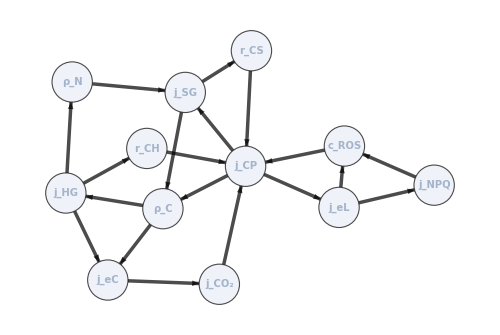

```mathematica
(*pairs of position in adjacency matrix and corresponding flux*)
numbers=Transpose[{Range@Length@#,#}]&@tsolve[[All,1]];
(*replacement rule to replace positions in adjacency matrix with flux names*)
fluxtonumber=#[[2]]->#[[1]]&/@numbers;
(*make a graph from the fluxes in tsolve (using the adjency matrix), for later: mark all markeds yellow*)graph[matrix_,markeds_]:=AdjacencyGraph[Transpose@matrix,VertexStyle->Table[i->Piecewise[{{Yellow, MemberQ[markeds/.fluxtonumber,i]}, {Lighter[ColorData[97][1],.9], True}}],
{i,Length@tsolve}],VertexSize->{{.2,.2}},VertexLabels->(#[[1]]->Placed[#[[2]],Center]&/@numbers/.names),VertexLabelStyle->Directive[10,Bold,Italic],ImageSize->500,EdgeStyle->{{Thickness[Scaled[.005]],Black}},GraphLayout->{"SpringEmbedding","RandomSeed"->6},DirectedEdges->True];
graph[matrix,{}]
```

```mathematica
(*adjacency matrix when fluxes at the positions columns are bufferd: set columns to 0*)
reducematrix[columns_]:=ReplacePart[matrix,Table[{i_,column}->0,{column,columns}]];
(*test if graph is acyclic (and in Mathematica terms has has no self loops)*)
GoodGraphQ:=AcyclicGraphQ[#]∧LoopFreeGraphQ[#]&;
(*get all possible flux combinations up to level*)
acycliccombinations[level_]:=Subsets[tsolve[[All,1]],level];
(*find all combinations with a given number of fluxes as state variables (maximally maxlevel) that make the graph having no cycles. Exclude redundant solutions (that just add state variables to lower level solutions)*)
maxlevel=7;
Clear[fluxsolutions];
Table[fluxsolutions[level]=Table[If[GoodGraphQ[graph[reducematrix[statefluxes/.fluxtonumber],{}]],statefluxes,Nothing],{statefluxes,Select[acycliccombinations[{level}],If[level==0,True,And@@Table[Not@SubsetQ[#,lowersolution],{lowersolution,Flatten[Table[fluxsolutions[lowerlevel],{lowerlevel,0,level-1}],1]}]]&]}],{level,0,maxlevel}];
```

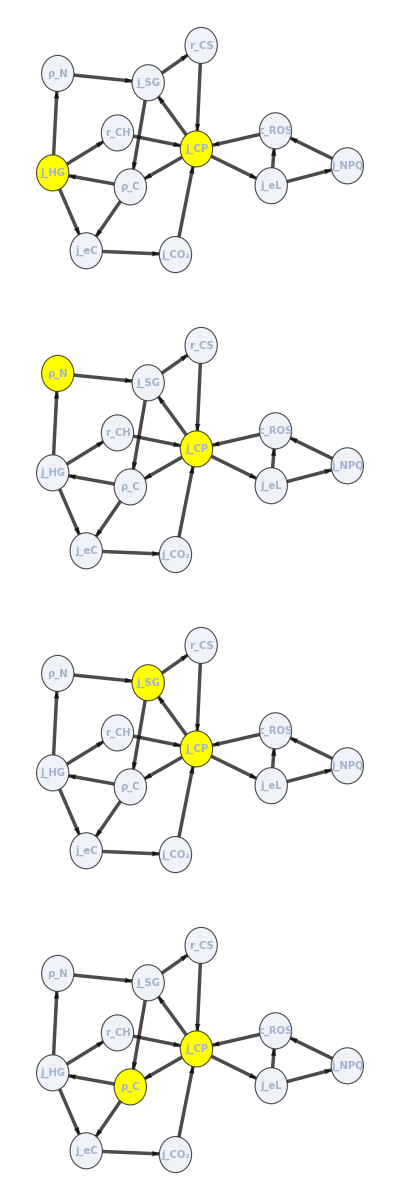
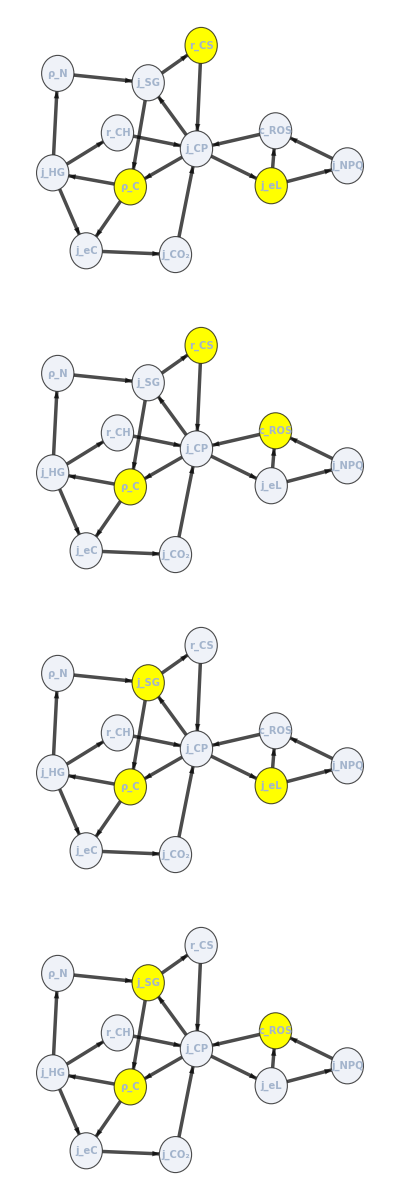
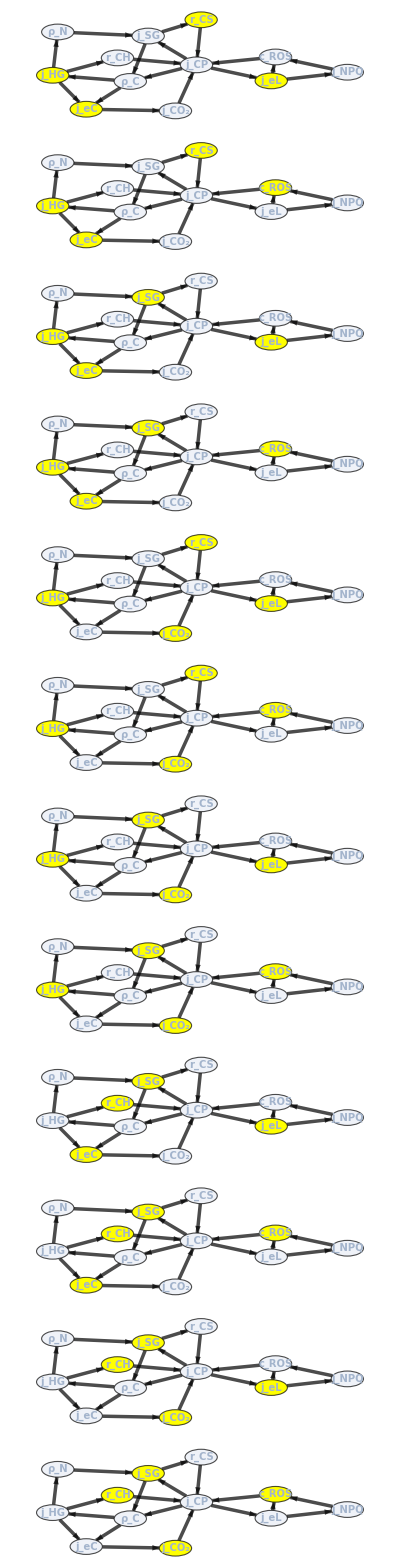
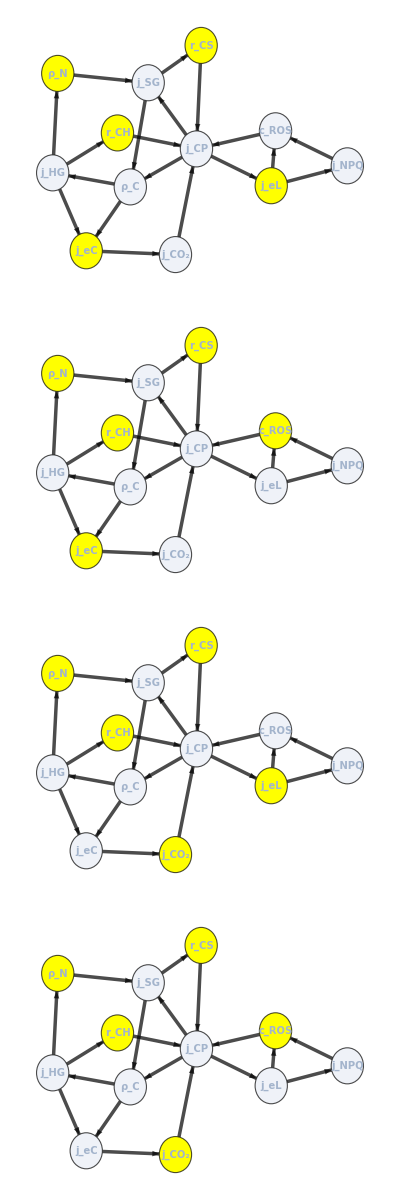
Symbiont-host coral model. Cycle-free versions of graph for the auxiliary variables. Yellow: auxiliary variables that when buffered interrupt all cycles in the graph.
Do not show redundant solutions (that just add buffers to ready solutions with less buffers).
--------------
Number of buffers: 0

--------------
Number of buffers: 1

--------------
Number of buffers: 2
-Graphics-
--------------
Number of buffers: 3
-Graphics-
--------------
Number of buffers: 4
-Graphics-
--------------
Number of buffers: 5
-Graphics-
--------------
Number of buffers: 6

--------------
Number of buffers: 7

```mathematica
(Export[NotebookDirectory[]<>"fluxplots-corals.pdf",#];#)&@Column[Join[{TextCell["Symbiont-host coral model. Cycle-free versions of graph for the auxiliary variables. Yellow: auxiliary variables that when buffered interrupt all cycles in the graph.\nDo not show redundant solutions (that just add buffers to ready solutions with less buffers)."]},Table[
Column[{"--------------",Row[{"Number of buffers: ",level}],
Column[Table[graph[matrix,statefluxes],{statefluxes,fluxsolutions[level]}]]}],
{level,0,maxlevel}]]]
```